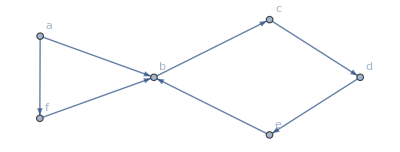

```mathematica
Graph[{a,b,c,d,e,f},{a->b,b->c,c->d,d->e,e->b,a->f,f->b},VertexLabels->Automatic]
```

Checking the graph is not Eulerian:

```mathematica
EulerianGraphQ[Graph[{a,b,c,d,e,f},{a->b,b->c,c->d,d->e,e->b,a->f,f->b},VertexLabels->Automatic]]
```

False

```mathematica
Graph[{a,b,c,d,e,f},{a->b,b->c,c->d,d->e,e->b,a->f,f->b},VertexLabels->Automatic,ImageSize->Full]
```

-Graphics-

```mathematica
FileNameJoin[{NotebookDirectory[],"even directed graph that is not Eulerian counterexample.svg"}]
```

C:\Users\peter\Documents\GitHub\data-visualization-functions\even directed graph that is not Eulerian counterexample.svg

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"even directed graph that is not Eulerian counterexample.svg"}],Graph[{a,b,c,d,e,f},{a->b,b->c,c->d,d->e,e->b,a->f,f->b},VertexLabels->Automatic,ImageSize->Full]]
```

C:\Users\peter\Documents\GitHub\data-visualization-functions\even directed graph that is not Eulerian counterexample.svg

```mathematica
SystemOpen["C:\\Users\\peter\\Documents\\GitHub\\data-visualization-functions\\even directed graph that is not Eulerian counterexample.svg"]
```

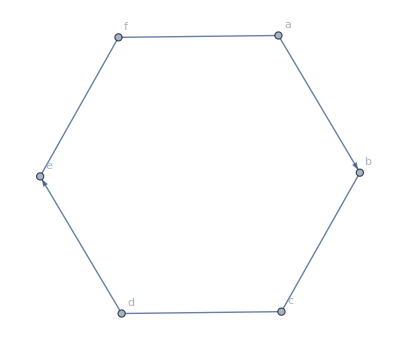

```mathematica
Graph[{a,b,c,d,e,f},{a->b,b<->c,c<->d,d->e,e<->f,a<->f},VertexLabels->Automatic,ImageSize->Full]
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"Eulerian mixed graph that is even but not symmetric proving that evenness and symmetricness is not a necessary and sufficient condition for a mixed graph to be Eulerian.svg"}],Graph[{a,b,c,d,e,f},{a->b,b<->c,c<->d,d->e,e<->f,a<->f},VertexLabels->Automatic,ImageSize->Full]]
```

C:\Users\peter\Documents\GitHub\data-visualization-functions\Eulerian mixed graph that is even but not symmetric proving that evenness and symmetricness is not a necessary and sufficient condition for a mixed graph to be Eulerian.svg

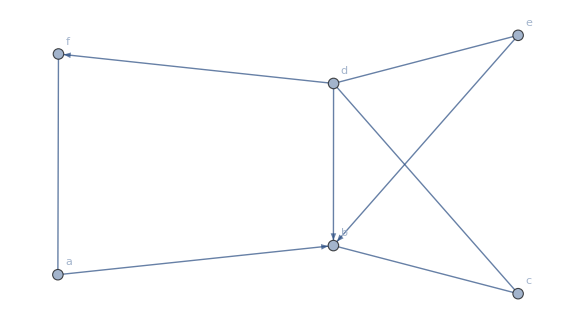

```mathematica
Graph[{a->b,b<->c,c<->d,d->b,d<->e,d->f,f<->a,e->b},VertexLabels->Automatic,ImageSize->Large]
```

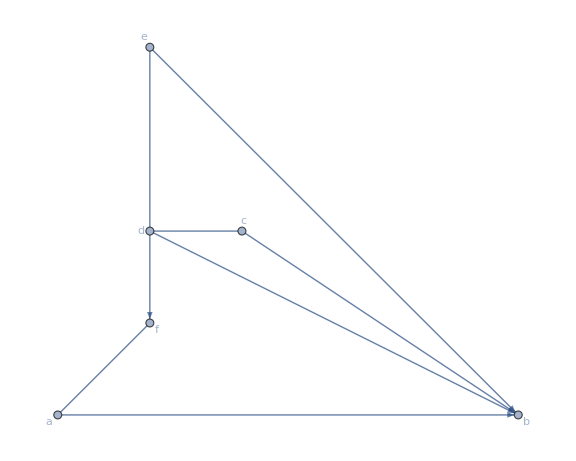

```mathematica
Graph[{a->b,b<->c,c<->d,d->b,d<->e,d->f,f<->a,e->b},VertexLabels->Automatic,ImageSize->Large,GraphLayout->"PlanarEmbedding"]
```

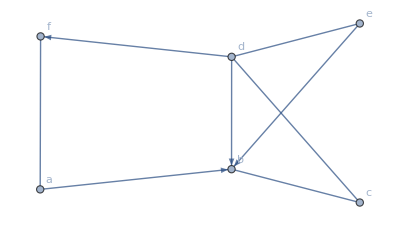

```mathematica
Graph[{a->b,b<->c,c<->d,d->b,d<->e,d->f,f<->a,e->b},VertexLabels->Automatic,ImageSize->Full]
```

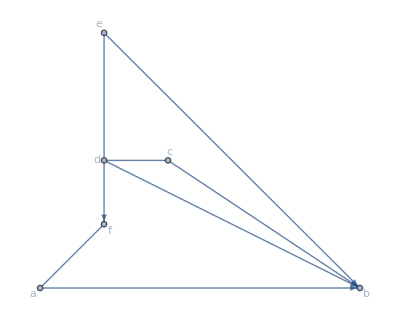

```mathematica
Graph[{a->b,b<->c,c<->d,d->b,d<->e,d->f,f<->a,e->b},VertexLabels->Automatic,ImageSize->Full,GraphLayout->"PlanarEmbedding"]
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"even mixed graph that violates the balanced set condition and is therefor not Eulerian.svg"}],Graph[{a->b,b<->c,c<->d,d->b,d<->e,d->f,f<->a,e->b},VertexLabels->Automatic,ImageSize->Full,GraphLayout->"PlanarEmbedding"]]
```

C:\Users\peter\Documents\GitHub\data-visualization-functions\even mixed graph that violates the balanced set condition and is therefor not Eulerian.svg

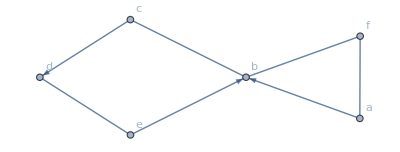

```mathematica
Graph[{a,b,c,d,e,f},{a->b,b<->c,c->d,d<->e,e->b,a<->f,f<->b},VertexLabels->Automatic,ImageSize->Full]
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"even mixed graph satisfies the balanced set condition and is therefore an Eulerian mixed graph.svg"}],Graph[{a,b,c,d,e,f},{a->b,b<->c,c->d,d<->e,e->b,a<->f,f<->b},VertexLabels->Automatic,ImageSize->Full]]
```

C:\Users\peter\Documents\GitHub\data-visualization-functions\even mixed graph satisfies the balanced set condition and is therefore an Eulerian mixed graph.svg